```mathematica
SetOptions[Graphics,BaseStyle->{FontFamily->"Braciola MS Extrabold",FontSize->85},PlotRangePadding->None,ImagePadding->None,ImageSize->168,PlotRange->{{-0.6,0.6},{-0.6,0.6}}]
```

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{FontFamily→Braciola MS Extrabold,FontSize→85},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→None,ImageSize→168,ImageSizeRaw→Automatic,LabelStyle→{},Method→Automatic,PlotLabel→None,PlotRange→{{-0.6,0.6},{-0.6,0.6}},PlotRangeClipping→False,PlotRangePadding→None,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

```mathematica
creamColor=Lighter[RGBColor[{255,248,209}/255]];
```

```mathematica
GenerateFid[id_]:=With[{idChars=Characters[id],ofst=0.19,col=White},
Graphics[{col,Rectangle[{-0.6,-0.6},{0.6,0.6}],Black,Rectangle[{-0.5,-0.5},{0.5,0.5}],col,Rectangle[{-0.4,-0.4},{0.4,0.4}],Black,Text[idChars⟦1⟧,{-ofst,ofst}],Text[idChars⟦2⟧,{ofst,ofst}],Text[idChars⟦3⟧,{-ofst,-ofst}],Text[idChars⟦4⟧,{ofst,-ofst}]}]
];
```

```mathematica
ids={"896F","CB64","FA6F","DF64","9261","B41B","BD2D","4327","6B6F","6C66","0029","BCB5","9669","    ","    ","    "};
```

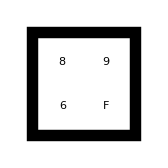

```mathematica
fids=GenerateFid/@ids;
fids⟦1⟧
```

```mathematica
Function[id,Export["C:\\Users\\John K\\Documents\\GitHub\\cu-droplet\\other_code\\DropletMotionTracking\\fids4\\"<>id<>".bmp",GenerateFid[id]]]/@ids⟦;;-4⟧
Export["C:\\Users\\John K\\Documents\\GitHub\\cu-droplet\\other_code\\DropletMotionTracking\\fids4\\"<>"ROOT"<>".bmp",GenerateFid["    "]]
```

{C:\Users\John K\Documents\GitHub\cu-droplet\other_code\DropletMotionTracking\fids4\896F.bmp,C:\Users\John K\Documents\GitHub\cu-droplet\other_code\DropletMotionTracking\fids4\CB64.bmp,C:\Users\John K\Documents\GitHub\cu-droplet\other_code\DropletMotionTracking\fids4\FA6F.bmp,C:\Users\John K\Documents\GitHub\cu-droplet\other_code\DropletMotionTracking\fids4\DF64.bmp,C:\Users\John K\Documents\GitHub\cu-droplet\other_code\DropletMotionTracking\fids4\9261.bmp,C:\Users\John K\Documents\GitHub\cu-droplet\other_code\DropletMotionTracking\fids4\B41B.bmp,C:\Users\John K\Documents\GitHub\cu-droplet\other_code\DropletMotionTracking\fids4\BD2D.bmp,C:\Users\John K\Documents\GitHub\cu-droplet\other_code\DropletMotionTracking\fids4\4327.bmp,C:\Users\John K\Documents\GitHub\cu-droplet\other_code\DropletMotionTracking\fids4\6B6F.bmp,C:\Users\John K\Documents\GitHub\cu-droplet\other_code\DropletMotionTracking\fids4\6C66.bmp,C:\Users\John K\Documents\GitHub\cu-droplet\other_code\DropletMotionTracking\fids4\0029.bmp,C:\Users\John K\Documents\GitHub\cu-droplet\other_code\DropletMotionTracking\fids4\BCB5.bmp,C:\Users\John K\Documents\GitHub\cu-droplet\other_code\DropletMotionTracking\fids4\9669.bmp}

C:\Users\John K\Documents\GitHub\cu-droplet\other_code\DropletMotionTracking\fids4\ROOT.bmp

C:\Users\John K\Documents\GitHub\cu-droplet\other_code\DropletMotionTracking\Fids4\896F.bmp

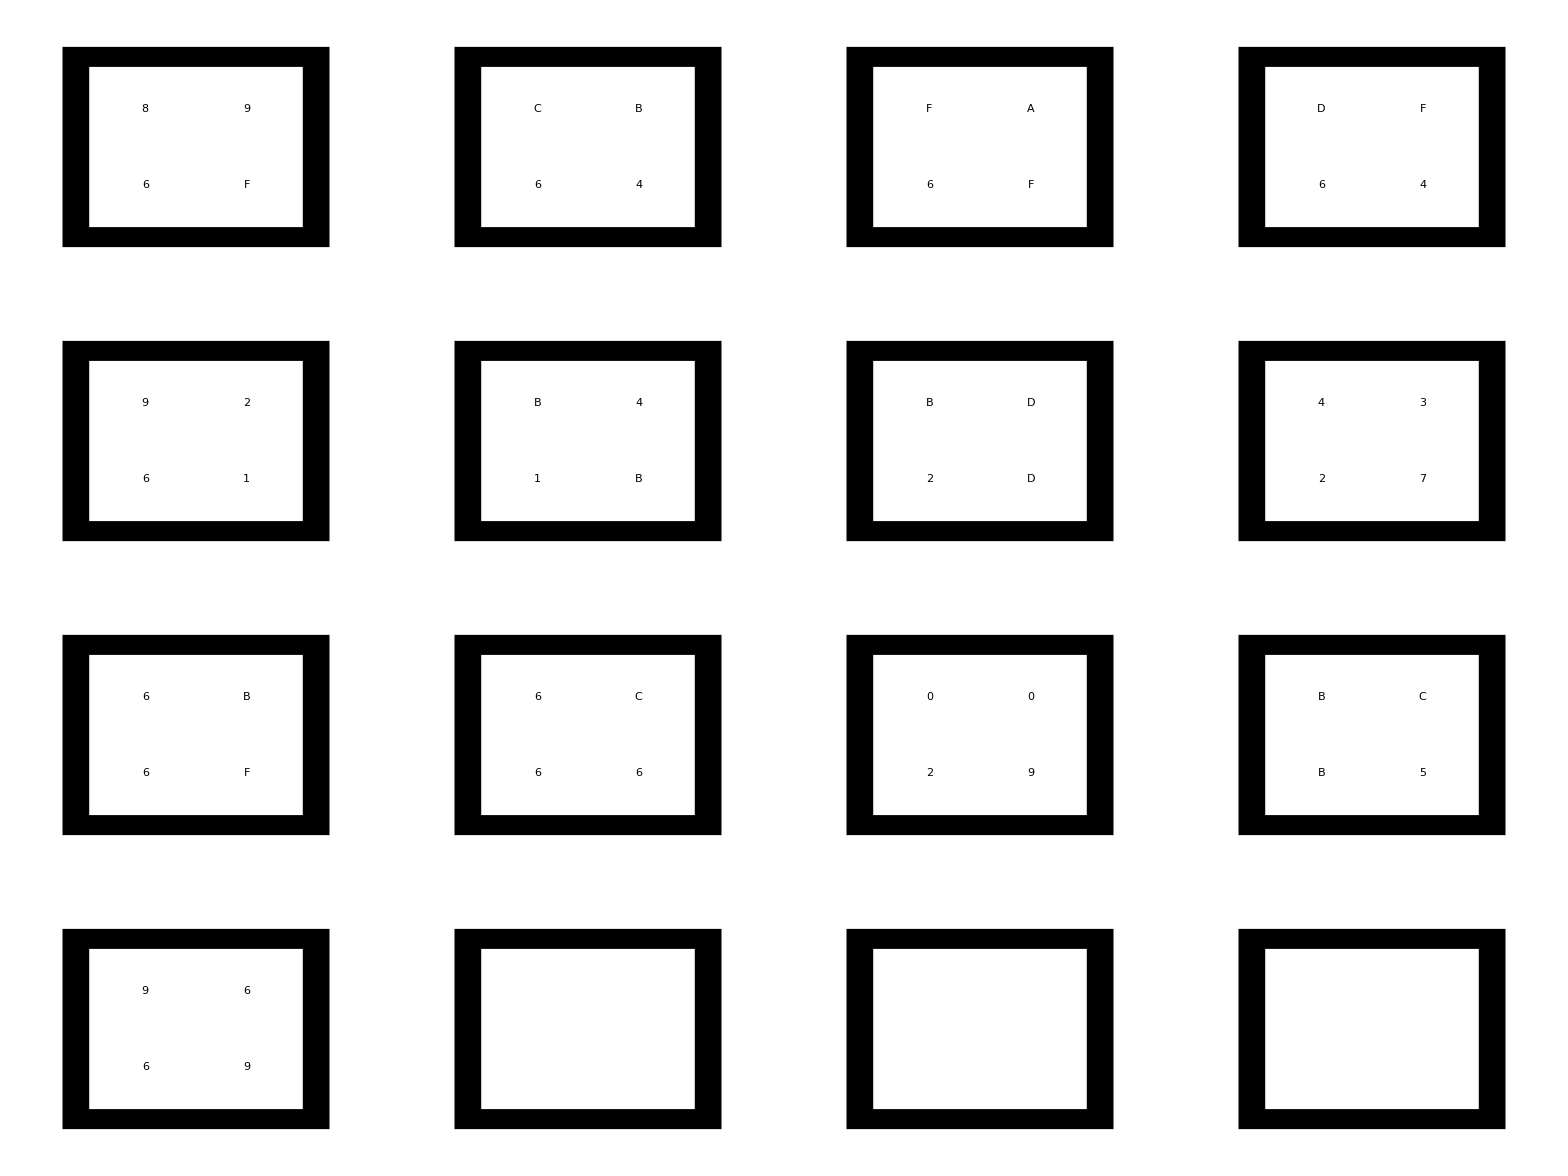

```mathematica
allFids=Grid[Partition[fids,4],Dividers->All,FrameStyle->Directive[{Dashed,Opacity[0.5]}],Spacings->{0,0}]
```

```mathematica
Export["C:\\Users\\John K\\Documents\\GitHub\\cu-droplet\\other_code\\DropletMotionTracking\\test.pdf",allFids]
```

C:\Users\John K\Documents\GitHub\cu-droplet\other_code\DropletMotionTracking\test.pdf